### Start choosing the example:

```mathematica
t=30;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
Data["Switching Costs"]={}
```

{}

```mathematica
Data
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 2, U1-> 0}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.007463,Null}

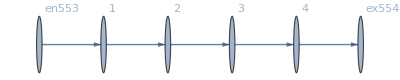

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→6.,u574→4.,u575→2.,u576→0,u577→6.,u578→-2+6.,u579→-2+4.,u580→-2+2.,u581→0,u582→6.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→3.13959,u574→2.09306,u575→1.04653,u576→0,u577→0.+1. 3.13959,u578→0.+1. 2.09306,u579→0.+1. 1.04653,u580→0,u581→0,u582→0.+1. 3.13959|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 3.84593×10^-16

FRX1: The Error on the nonlinear terms is 3.84593×10^-16

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→3.2972,u574→2.19814,u575→1.09907,u576→0,u577→0.+1. 3.2972,u578→0.+1. 2.19814,u579→0.+1. 1.09907,u580→0,u581→0,u582→0.+1. 3.2972|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→3.66483,u574→2.44322,u575→1.22161,u576→0,u577→0.+1. 3.66483,u578→0.+1. 2.44322,u579→0.+1. 1.22161,u580→0,u581→0,u582→0.+1. 3.66483|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 4.44089×10^-16

FRX1: The Error on the nonlinear terms is 4.44089×10^-16

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→5.50047,u574→3.66698,u575→1.83349,u576→0,u577→0.+1. 5.50047,u578→0.+1. 3.66698,u579→0.+1. 1.83349,u580→0,u581→0,u582→0.+1. 5.50047|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 3.84593×10^-15

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→6.,u574→4.,u575→2.,u576→0,u577→0.+1. 6.,u578→0.+1. 4.,u579→0.+1. 2.,u580→0,u581→0,u582→0.+1. 6.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 7.69185×10^-16

FRX1: The Error on the nonlinear terms is 7.69185×10^-16

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→7.32794,u574→4.88529,u575→2.44265,u576→0,u577→0.+1. 7.32794,u578→0.+1. 4.88529,u579→0.+1. 2.44265,u580→0,u581→0,u582→0.+1. 7.32794|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 7.69185×10^-16

FRX1: The Error on the nonlinear terms is 7.69185×10^-16

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→10.9282,u574→7.28546,u575→3.64273,u576→0,u577→0.+1. 10.9282,u578→0.+1. 7.28546,u579→0.+1. 3.64273,u580→0,u581→0,u582→0.+1. 10.9282|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→13.0372,u574→8.69147,u575→4.34573,u576→0,u577→0.+1. 13.0372,u578→0.+1. 8.69147,u579→0.+1. 4.34573,u580→0,u581→0,u582→0.+1. 13.0372|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→13.0397,u574→8.69314,u575→4.34657,u576→0,u577→0.+1. 13.0397,u578→0.+1. 8.69314,u579→0.+1. 4.34657,u580→0,u581→0,u582→0.+1. 13.0397|>

```mathematica
alpha = 2;
FixedPoint[FixedReduceX1[MFGEquations],FFR,10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 6.15348×10^-15

FRX1: The Error on the nonlinear terms is 6.15348×10^-15

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→49.1196,u574→32.7464,u575→16.3732,u576→0,u577→0.+1. 49.1196,u578→0.+1. 32.7464,u579→0.+1. 16.3732,u580→0,u581→0,u582→0.+1. 49.1196|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→13.1636,u574→8.77571,u575→4.38786,u576→0,u577→0.+1. 13.1636,u578→0.+1. 8.77571,u579→0.+1. 4.38786,u580→0,u581→0,u582→0.+1. 13.1636|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→13.2923,u574→8.86156,u575→4.43078,u576→0,u577→0.+1. 13.2923,u578→0.+1. 8.86156,u579→0.+1. 4.43078,u580→0,u581→0,u582→0.+1. 13.2923|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→13.5573,u574→9.03823,u575→4.51911,u576→0,u577→0.+1. 13.5573,u578→0.+1. 9.03823,u579→0.+1. 4.51911,u580→0,u581→0,u582→0.+1. 13.5573|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→14.4175,u574→9.61169,u575→4.80584,u576→0,u577→0.+1. 14.4175,u578→0.+1. 9.61169,u579→0.+1. 4.80584,u580→0,u581→0,u582→0.+1. 14.4175|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→16.1117,u574→10.7411,u575→5.37057,u576→0,u577→0.+1. 16.1117,u578→0.+1. 10.7411,u579→0.+1. 5.37057,u580→0,u581→0,u582→0.+1. 16.1117|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→20.9727,u574→13.9818,u575→6.99091,u576→0,u577→0.+1. 20.9727,u578→0.+1. 13.9818,u579→0.+1. 6.99091,u580→0,u581→0,u582→0.+1. 20.9727|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→29.6824,u574→19.7883,u575→9.89413,u576→0,u577→0.+1. 29.6824,u578→0.+1. 19.7883,u579→0.+1. 9.89413,u580→0,u581→0,u582→0.+1. 29.6824|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 6.15348×10^-15

FRX1: The Error on the nonlinear terms is 6.15348×10^-15

<|j555→2,j556→2,j557→2,j558→2,j559→2,j560→0,j561→0,j562→0,j563→0,j564→0,jt565→0,jt566→2,jt567→2,jt568→0,jt569→2,jt570→0,jt571→2,jt572→0,u573→49.1196,u574→32.7464,u575→16.3732,u576→0,u577→0.+1. 49.1196,u578→0.+1. 32.7464,u579→0.+1. 16.3732,u580→0,u581→0,u582→0.+1. 49.1196|>

### What we this plot for?

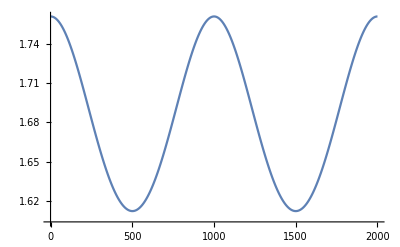

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.